# Birkhoff Normal Form : SU(3) & 1-Holed Torus

## By: Forni, Goldman, Lawton, Matheus Last Edited: June 2022

## Step 1: Trace coordinates.

## Trace Coordinates on SL(3, ℂ) & SU(3) Character Varieties of Rank 2 Free Group

#### Please set the directory to where ever you put this file and the companion file "outer.m".

```mathematica
SetDirectory["~/Dropbox/Publications/Projects/KAM-CharVar/Mathematica"];
<<outer.m
```

#### Example of using the Word and TracePoly commands:

```mathematica
S
```

{t[1],t[2],t[3],t[-1],t[-2],t[-3],t[4],t[-4],t[5]}

```mathematica
TracePoly[Word[1,2,2,2],S]
```

t[1]-t[-2] t[1] t[2]-t[-2] t[3]+t[2]^2 t[3]+t[2] t[4]

#### Query with ? the commands in outer.m:

```mathematica
?Word
```

```mathematica
?TracePoly
```

```mathematica
?S
```

#### Readable Notation Substitution:

```mathematica
RNS={t[1]->x,t[-1]->X,t[2]->y,t[-2]->Y,t[3]->z,t[-3]->Z,t[4]->t,t[-4]->T,t[5]->v};
URNS={u[1]->x,u[-1]->X,u[2]->y,u[-2]->Y,u[3]->z,u[-3]->Z,u[4]->t,u[-4]->T,u[5]->v};
```

```mathematica
TracePoly[Word[1,2,2,2],S]/.RNS
```

x+t y-x y Y+y^2 z-Y z

#### Evaluation maps Hom(F_2,G)→Hom(F_2 G)//G for SL(3, ℂ) & SU(3).

```mathematica
Comm[A_,B_]:=A.B.Inverse[A].Inverse[B];
Cartan[A_]:=Conjugate[Transpose[A]];
Subscript[T, 1][A_,B_]:=Tr[A];
Subscript[T, -1][A_,B_]:=Tr[Inverse[A]];
Subscript[T, 2][A_,B_]:=Tr[B];
Subscript[T, -2][A_,B_]:=Tr[Inverse[B]];
Subscript[T, 3][A_,B_]:=Tr[A.B];
Subscript[T, -3][A_,B_]:=Tr[Inverse[A].Inverse[B]];
Subscript[T, 4][A_,B_]:=Tr[A.Inverse[B]];
Subscript[T, -4][A_,B_]:=Tr[Inverse[A].B]
Subscript[T, 5][A_,B_]:=Tr[Comm[A,B]];
Subscript[T, -5][A_,B_]:=Tr[Comm[B,A]];
Sub[{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_}]:={t[1]->a,t[-1]->b,t[2]->c,t[-2]->d,t[3]->e,t[-3]->f,t[4]->g,t[-4]->h,t[5]-> i,t[-5]->j};
USub[{a_,b_,c_,d_,e_,f_,g_,h_,i_}]:={u[1]->a,u[-1]->b,u[2]->c,u[-2]->d,u[3]->e,u[-3]->f,u[4]->g,u[-4]->h,u[5]-> i};
Hom[A_,B_]:={Subscript[T, 1][A,B],Subscript[T, -1][A,B],Subscript[T, 2][A,B],Subscript[T, -2][A,B],Subscript[T, 3][A,B],Subscript[T, -3][A,B],Subscript[T, 4][A,B],Subscript[T, -4][A,B],Subscript[T, 5][A,B],Subscript[T, -5][A,B]};
UHom[A_,B_]:={Re[Subscript[T, 1][A,B]],Im[Subscript[T, 1][A,B]],Re[Subscript[T, 2][A,B]],Im[Subscript[T, 2][A,B]],Re[Subscript[T, 3][A,B]],Im[Subscript[T, 3][A,B]],Re[Subscript[T, 4][A,B]],Im[Subscript[T, 4][A,B]],Im[Subscript[T, 5][A,B]]};
TrEv[{A_,B_}]:=Sub[Hom[A,B]];
UTrEv[{A_,B_}]:=USub[UHom[A,B]];
C1=DiagonalMatrix[{Subscript[c1, 1],Subscript[c1, 2],1/(Subscript[c1, 1]*Subscript[c1, 2])}];
C2=Table[Subscript[c2, i,j],{i,1,3},{j,1,3}]/.{Subscript[c2, 3,1]->(-1+Subscript[c2, 1,3] Subscript[c2, 2,1] Subscript[c2, 3,2]-Subscript[c2, 1,1] Subscript[c2, 2,3] Subscript[c2, 3,2]-Subscript[c2, 1,2] Subscript[c2, 2,1] Subscript[c2, 3,3]+Subscript[c2, 1,1] Subscript[c2, 2,2] Subscript[c2, 3,3])/(Subscript[c2, 1,3] Subscript[c2, 2,2]-Subscript[c2, 1,2] Subscript[c2, 2,3])};
CRep={C1,C2};
D1=DiagonalMatrix[{Exp[I*Subscript[d1, 1]],Exp[I*Subscript[d1, 2]],Exp[-I*(Subscript[d1, 1]+Subscript[d1, 2])]}];
D2={{Cos[Subscript[d2, 1]]Cos[Subscript[d2, 2]]Exp[I*Subscript[d2, 4]],Sin[Subscript[d2, 1]]Exp[I*Subscript[d2, 6]],Cos[Subscript[d2, 1]]Sin[Subscript[d2, 2]]Exp[I*Subscript[d2, 7]]},{Sin[Subscript[d2, 2]]Sin[Subscript[d2, 3]]Exp[-I*(Subscript[d2, 7]+Subscript[d2, 8])]-Sin[Subscript[d2, 1]]Cos[Subscript[d2, 2]]Cos[Subscript[d2, 3]]Exp[I*(Subscript[d2, 4]+Subscript[d2, 5]-Subscript[d2, 6])],Cos[Subscript[d2, 1]]Cos[Subscript[d2, 3]]Exp[I*Subscript[d2, 5]],-Cos[Subscript[d2, 2]]Sin[Subscript[d2, 3]]Exp[-I*(Subscript[d2, 4]+Subscript[d2, 8])]-Sin[Subscript[d2, 1]]Sin[Subscript[d2, 2]]Cos[Subscript[d2, 3]]Exp[I*(Subscript[d2, 5]-Subscript[d2, 6]+Subscript[d2, 7])]},{-Sin[Subscript[d2, 1]]Cos[Subscript[d2, 2]]Sin[Subscript[d2, 3]]Exp[I*(Subscript[d2, 4]-Subscript[d2, 6]+Subscript[d2, 8])]-Sin[Subscript[d2, 2]]Cos[Subscript[d2, 3]]Exp[-I*(Subscript[d2, 5]+Subscript[d2, 7])],Cos[Subscript[d2, 1]]Sin[Subscript[d2, 3]]Exp[I*Subscript[d2, 8]],Cos[Subscript[d2, 2]]Cos[Subscript[d2, 3]]Exp[-I*(Subscript[d2, 4]+Subscript[d2, 5])]-Sin[Subscript[d2, 1]]Sin[Subscript[d2, 2]]Sin[Subscript[d2, 3]]Exp[I*(-Subscript[d2, 6]+Subscript[d2, 7]+Subscript[d2, 8])]}};
DRep={D1,D2};
```

```mathematica
Simplify[Det[C1]]
Simplify[Det[C2]]
```

1

1

```mathematica
FullSimplify[ComplexExpand[D2.Conjugate[Transpose[D2]]]]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
FullSimplify[Det[D1]]
FullSimplify[Det[D2]]
```

1

1

```mathematica
Simplify[(P-t[5]-t[-5])/.TrEv[CRep]]
```

0

```mathematica
Simplify[(Q-t[5]*t[-5])/.TrEv[CRep]]
```

0

## Step 2: Cat map on SU(3)-character variety.

## Global coordinates on (SU(3))^2/SU(3)≈S^8

### u_1=ReTr(A), v_1=ImTr(A), u_2=ReTr(B), v_2=ImTr(B), u_3=ReTr(AB), v_3=ImTr(AB), u_4 = ReTr(AB^-1), v_4=ImTr(AB^-1), u_5=ImTr([A,B]), v_5=ReTr([A,B]). Remark: We do not use v_5 in the calculations below since it equals P/2. Note: the reason why we use "u" for the 5th coordinate and not "v" is because Florentino-Lawton did that in their Mathematische Annalen paper. The imaginary part of the trace of the commutator is the only part that matters since the real part is P/2 and hence determined by the other 8 coordinates. So they chose to call the part that was important "u_5" even though it is inconsistent with the notation for the other 8 coordinates. T_A(B)=BA, T_A(A)=A, T_B(B)=B, & T_B(A)=AB. T_A⟷ {{1,1},{0,1}} and T_B⟷ {{1,0},{1,1}}. T_A∘T_B is the CAT map.

```mathematica
{{1,1},{0,1}}.{{1,0},{1,1}}//MatrixForm
```

(2 | 1
1 | 1)

```mathematica
TASU3[{u1_,v1_,u2_,v2_,u3_,v3_,u4_,v4_,u5_}]:={u1,v1,u3,v3,-u1*u2+u1*u3+u4-v1*v2-v1*v3, u2*v1+u3*v1-u1*v2+u1*v3-v4,u2,-v2,u5};
TBSU3[{u1_,v1_,u2_,v2_,u3_,v3_,u4_,v4_,u5_}]:={u3,v3,u2,v2,-u1*u2+u2*u3+u4-v1*v2-v2*v3,-u2*v1+u1*v2+u3*v2+u2*v3+v4,u1,v1,u5};
CATSU3[{u1_,v1_,u2_,v2_,u3_,v3_,u4_,v4_,u5_}]:=FullSimplify[TASU3[TBSU3[{u1,v1,u2,v2,u3,v3,u4,v4,u5}]]];
```

```mathematica
Expand[CATSU3[{x,X,y,Y,z,Z,t,T,v}]]
```

{z,Z,t-x y-X Y+y z-Y Z,T-X y+x Y+Y z+y Z,x+t z-y z-x y z-X Y z+y z^2-T Z+X y Z-Y Z-x Y Z-2 Y z Z-y Z^2,-X+T z-X y z-Y z+x Y z+Y z^2+t Z+y Z-x y Z-X Y Z+2 y z Z-Y Z^2,y,-Y,v}

## Step 3: P, Q & Boundary map (in unitary coordinates)

## Unitary Coordinates

```mathematica
PU=ComplexExpand[P/2/.{t[1]->u[1]+I*u[-1],t[2]->u[2]+I*u[-2],t[3]->u[3]+I*u[-3],t[4]->u[4]+I*u[-4],t[-1]->u[1]-I*u[-1],t[-2]->u[2]-I*u[-2],t[-3]->u[3]-I*u[-3],t[-4]->u[4]-I*u[-4]}];
```

```mathematica
T2U={t[1]->u[1]+I*u[-1],t[2]->u[2]+I*u[-2],t[3]->u[3]+I*u[-3],t[4]->u[4]+I*u[-4],t[-1]->u[1]-I*u[-1],t[-2]->u[2]-I*u[-2],t[-3]->u[3]-I*u[-3],t[-4]->u[4]-I*u[-4],t[5]->I*u[5]+PU};
U2T={u[1]->(t[1]+t[-1])/2,u[-1]->(t[1]-t[-1])/(2*I),u[2]->(t[2]+t[-2])/2,u[-2]->(t[2]-t[-2])/(2*I),u[3]->(t[3]+t[-3])/2,u[-3]->(t[3]-t[-3])/(2*I),u[4]->(t[4]+t[-4])/2,u[-4]->(t[4]-t[-4])/(2*I),u[5]->(2*t[5]-P)/(2*I)};
```

```mathematica
QU=ComplexExpand[Q/.T2U]
```

9-6 u[-4]^2-6 u[-3]^2+u[-4]^2 u[-3]^2+2 u[-4]^2 u[-3] u[-2]-2 u[-4] u[-3]^2 u[-2]-6 u[-2]^2+u[-4]^2 u[-2]^2-2 u[-4] u[-3] u[-2]^2+u[-3]^2 u[-2]^2+2 u[-4]^2 u[-3] u[-1]+2 u[-4] u[-3]^2 u[-1]+4 u[-4]^2 u[-2] u[-1]-4 u[-3]^2 u[-2] u[-1]-2 u[-4] u[-2]^2 u[-1]-2 u[-3] u[-2]^2 u[-1]-6 u[-1]^2+u[-4]^2 u[-1]^2+2 u[-4] u[-3] u[-1]^2+u[-3]^2 u[-1]^2+2 u[-4] u[-2] u[-1]^2-2 u[-3] u[-2] u[-1]^2+u[-2]^2 u[-1]^2+u[-2]^4 u[-1]^2+u[-2]^2 u[-1]^4+6 u[-4] u[-3] u[1]-6 u[-4] u[-2] u[1]+6 u[-3] u[-2] u[1]+2 u[-4] u[-3] u[-2]^2 u[1]+2 u[-4] u[-2]^3 u[1]-2 u[-3] u[-2]^3 u[1]+4 u[-4] u[-2]^2 u[-1] u[1]+4 u[-3] u[-2]^2 u[-1] u[1]-6 u[-1]^2 u[1]+2 u[-4] u[-2] u[-1]^2 u[1]-2 u[-3] u[-2] u[-1]^2 u[1]+6 u[-2]^2 u[-1]^2 u[1]-6 u[1]^2+u[-4]^2 u[1]^2-2 u[-4] u[-3] u[1]^2+u[-3]^2 u[1]^2-2 u[-4] u[-2] u[1]^2+2 u[-3] u[-2] u[1]^2+u[-2]^2 u[1]^2+u[-2]^4 u[1]^2+2 u[-2]^2 u[-1]^2 u[1]^2+2 u[1]^3+2 u[-4] u[-2] u[1]^3-2 u[-3] u[-2] u[1]^3-2 u[-2]^2 u[1]^3+u[-2]^2 u[1]^4-6 u[-4] u[-3] u[2]-6 u[-2]^2 u[2]+6 u[-4] u[-1] u[2]+6 u[-3] u[-1] u[2]-2 u[-4] u[-2]^2 u[-1] u[2]-2 u[-3] u[-2]^2 u[-1] u[2]-2 u[-4] u[-3] u[-1]^2 u[2]-4 u[-4] u[-2] u[-1]^2 u[2]+4 u[-3] u[-2] u[-1]^2 u[2]+6 u[-2]^2 u[-1]^2 u[2]-2 u[-4] u[-1]^3 u[2]-2 u[-3] u[-1]^3 u[2]+4 u[-4]^2 u[1] u[2]+4 u[-3]^2 u[1] u[2]+4 u[-4] u[-2] u[1] u[2]-4 u[-3] u[-2] u[1] u[2]-4 u[-4] u[-1] u[1] u[2]-4 u[-3] u[-1] u[1] u[2]-2 u[-4] u[-3] u[1]^2 u[2]+4 u[-4] u[-2] u[1]^2 u[2]-4 u[-3] u[-2] u[1]^2 u[2]+6 u[-2]^2 u[1]^2 u[2]-2 u[-4] u[-1] u[1]^2 u[2]-2 u[-3] u[-1] u[1]^2 u[2]-6 u[2]^2+u[-4]^2 u[2]^2+2 u[-4] u[-3] u[2]^2+u[-3]^2 u[2]^2+2 u[-4] u[-1] u[2]^2+2 u[-3] u[-1] u[2]^2+u[-1]^2 u[2]^2+2 u[-2]^2 u[-1]^2 u[2]^2+u[-1]^4 u[2]^2+2 u[-4] u[-3] u[1] u[2]^2+2 u[-4] u[-2] u[1] u[2]^2-2 u[-3] u[-2] u[1] u[2]^2-4 u[-4] u[-1] u[1] u[2]^2-4 u[-3] u[-1] u[1] u[2]^2+6 u[-1]^2 u[1] u[2]^2+u[1]^2 u[2]^2+2 u[-2]^2 u[1]^2 u[2]^2+2 u[-1]^2 u[1]^2 u[2]^2-2 u[1]^3 u[2]^2+u[1]^4 u[2]^2+2 u[2]^3-2 u[-4] u[-1] u[2]^3-2 u[-3] u[-1] u[2]^3-2 u[-1]^2 u[2]^3-2 u[1]^2 u[2]^3+u[-1]^2 u[2]^4+u[1]^2 u[2]^4-6 u[-3]^2 u[3]-6 u[-4] u[-2] u[3]+6 u[-4] u[-1] u[3]-6 u[-2] u[-1] u[3]+2 u[-4] u[-2]^2 u[-1] u[3]+2 u[-2]^3 u[-1] u[3]-2 u[-4] u[-2] u[-1]^2 u[3]+2 u[-2]^2 u[-1]^2 u[3]+2 u[-2] u[-1]^3 u[3]-2 u[-4]^2 u[1] u[3]+4 u[-4] u[-3] u[1] u[3]+8 u[-3] u[-2] u[1] u[3]-2 u[-2]^2 u[1] u[3]+4 u[-4] u[-1] u[1] u[3]+4 u[-2] u[-1] u[1] u[3]-2 u[-4] u[-2] u[1]^2 u[3]-2 u[-2]^2 u[1]^2 u[3]+2 u[-2] u[-1] u[1]^2 u[3]-2 u[-4]^2 u[2] u[3]-4 u[-4] u[-3] u[2] u[3]-4 u[-4] u[-2] u[2] u[3]+8 u[-3] u[-1] u[2] u[3]+4 u[-2] u[-1] u[2] u[3]-2 u[-1]^2 u[2] u[3]+6 u[1] u[2] u[3]-2 u[-2]^2 u[1] u[2] u[3]-8 u[-2] u[-1] u[1] u[2] u[3]-2 u[-1]^2 u[1] u[2] u[3]+2 u[1]^2 u[2] u[3]-2 u[1]^3 u[2] u[3]+2 u[-4] u[-1] u[2]^2 u[3]+2 u[-2] u[-1] u[2]^2 u[3]-2 u[-1]^2 u[2]^2 u[3]+2 u[1] u[2]^2 u[3]+2 u[1]^2 u[2]^2 u[3]-2 u[1] u[2]^3 u[3]-6 u[3]^2+u[-4]^2 u[3]^2+2 u[-4] u[-2] u[3]^2+u[-2]^2 u[3]^2-2 u[-4] u[-1] u[3]^2+4 u[-2] u[-1] u[3]^2+u[-1]^2 u[3]^2+u[1]^2 u[3]^2-4 u[1] u[2] u[3]^2+u[2]^2 u[3]^2+2 u[3]^3-6 u[-4]^2 u[4]+6 u[-3] u[-2] u[4]+6 u[-3] u[-1] u[4]+6 u[-2] u[-1] u[4]+2 u[-3] u[-2]^2 u[-1] u[4]-2 u[-2]^3 u[-1] u[4]+2 u[-3] u[-2] u[-1]^2 u[4]+2 u[-2]^2 u[-1]^2 u[4]-2 u[-2] u[-1]^3 u[4]+4 u[-4] u[-3] u[1] u[4]-2 u[-3]^2 u[1] u[4]-8 u[-4] u[-2] u[1] u[4]-2 u[-2]^2 u[1] u[4]+4 u[-3] u[-1] u[1] u[4]-4 u[-2] u[-1] u[1] u[4]+2 u[-3] u[-2] u[1]^2 u[4]-2 u[-2]^2 u[1]^2 u[4]-2 u[-2] u[-1] u[1]^2 u[4]-4 u[-4] u[-3] u[2] u[4]-2 u[-3]^2 u[2] u[4]+4 u[-3] u[-2] u[2] u[4]+8 u[-4] u[-1] u[2] u[4]-4 u[-2] u[-1] u[2] u[4]-2 u[-1]^2 u[2] u[4]+6 u[1] u[2] u[4]-2 u[-2]^2 u[1] u[2] u[4]+8 u[-2] u[-1] u[1] u[2] u[4]-2 u[-1]^2 u[1] u[2] u[4]+2 u[1]^2 u[2] u[4]-2 u[1]^3 u[2] u[4]+2 u[-3] u[-1] u[2]^2 u[4]-2 u[-2] u[-1] u[2]^2 u[4]-2 u[-1]^2 u[2]^2 u[4]+2 u[1] u[2]^2 u[4]+2 u[1]^2 u[2]^2 u[4]-2 u[1] u[2]^3 u[4]-4 u[-4] u[-2] u[3] u[4]+4 u[-3] u[-2] u[3] u[4]-2 u[-2]^2 u[3] u[4]+4 u[-4] u[-1] u[3] u[4]+4 u[-3] u[-1] u[3] u[4]-2 u[-1]^2 u[3] u[4]-6 u[1] u[3] u[4]-2 u[-2]^2 u[1] u[3] u[4]+2 u[1]^2 u[3] u[4]-6 u[2] u[3] u[4]-2 u[-1]^2 u[2] u[3] u[4]-2 u[1]^2 u[2] u[3] u[4]+2 u[2]^2 u[3] u[4]-2 u[1] u[2]^2 u[3] u[4]+2 u[1] u[3]^2 u[4]+2 u[2] u[3]^2 u[4]-6 u[4]^2+u[-3]^2 u[4]^2-2 u[-3] u[-2] u[4]^2+u[-2]^2 u[4]^2-2 u[-3] u[-1] u[4]^2-4 u[-2] u[-1] u[4]^2+u[-1]^2 u[4]^2+u[1]^2 u[4]^2-4 u[1] u[2] u[4]^2+u[2]^2 u[4]^2+2 u[1] u[3] u[4]^2+2 u[2] u[3] u[4]^2+u[3]^2 u[4]^2+2 u[4]^3

```mathematica
PU
```

-3/2+1/2 u[-4]^2+1/2 u[-3]^2+1/2 u[-2]^2+1/2 u[-1]^2+1/2 u[-2]^2 u[-1]^2+u[-4] u[-2] u[1]-u[-3] u[-2] u[1]+u[1]^2/2+1/2 u[-2]^2 u[1]^2-u[-4] u[-1] u[2]-u[-3] u[-1] u[2]+u[2]^2/2+1/2 u[-1]^2 u[2]^2+1/2 u[1]^2 u[2]^2+u[-2] u[-1] u[3]-u[1] u[2] u[3]+u[3]^2/2-u[-2] u[-1] u[4]-u[1] u[2] u[4]+u[4]^2/2

```mathematica
FullSimplify[ComplexExpand[P/.T2U]/2-PU]
```

0

## Step 4: Fixed Points

## Fixed points along the real line.

### Below is a family of fixed points in SU(3).

```mathematica
A[s_]:={{(s+I Sqrt[1-s^2])^2, 0, 0},{0,1,0},{0,0,(s-I Sqrt[1-s^2])^2}} ;
B[s_]:={{(s/(2s-1)+I (s/Sqrt[1-s^2])((1-s)/(2s-1)))^2,(s/(2s-1)+I (s/Sqrt[1-s^2])((1-s)/(2s-1)))(-Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2]),1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2},{2(s/(2s-1)+I (s/Sqrt[1-s^2])((1-s)/(2s-1)))(Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2]),(s/(2s-1)+I (s/Sqrt[1-s^2])((1-s)/(2s-1)))(s/(2s-1)-I (s/Sqrt[1-s^2])((1-s)/(2s-1)))+(-Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2])(Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2]),2(-Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2])(s/(2s-1)-I (s/Sqrt[1-s^2])((1-s)/(2s-1)))},{1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2,(Sqrt[1-(s/(2s-1))^2-((s/Sqrt[1-s^2])((1-s)/(2s-1)))^2])(s/(2s-1)-I (s/Sqrt[1-s^2])((1-s)/(2s-1))),(s/(2s-1)-I (s/Sqrt[1-s^2])((1-s)/(2s-1)))^2}};
```

```mathematica
FullSimplify[ComplexExpand[FullSimplify[UHom[A[s],B[s]],s∈Reals]]]
```

{-1+4 s^2,0,(-1+4 s)/(1-2 s)^2,0,-1+4 s^2,0,(-1+4 s)/(1-2 s)^2,0,0}

```mathematica
CATSU3[ComplexExpand[FullSimplify[UHom[A[s],B[s]],s∈Reals]]]
```

{-1+4 s^2,0,(-1+4 s)/(1-2 s)^2,0,-1+4 s^2,0,(-1+4 s)/(1-2 s)^2,0,0}

```mathematica
FullSimplify[ComplexExpand[FullSimplify[UHom[A[s],B[s]],s∈Reals]]-CATSU3[ComplexExpand[FullSimplify[UHom[A[s],B[s]],s∈Reals]]]]
```

{0,0,0,0,0,0,0,0,0}

### So this verifies that we have a line of fixed points in the free group character variety (SU(3) and F_2).

```mathematica
FullSimplify[PU/.USub[{-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,0}]]
```

((-3+4 s (3-6 s^2+4 s^3)) (-1+4 s (1+2 (-1+s) s (-1+2 s))))/(1-2 s)^4

```mathematica
FullSimplify[QU/.USub[{-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,0}]]
```

((3-4 s (3-6 s^2+4 s^3))^2 (1-4 s (1+2 (-1+s) s (-1+2 s)))^2)/(1-2 s)^8

```mathematica
ComplexExpand[FullSimplify[Subscript[T, 5][A[s],B[s]],s∈Reals]]
```

3/(1-2 s)^4-(24 s)/(1-2 s)^4+(24 s^2)/(1-2 s)^4+(192 s^3)/(1-2 s)^4-(448 s^4)/(1-2 s)^4+(64 s^5)/(1-2 s)^4+(704 s^6)/(1-2 s)^4-(768 s^7)/(1-2 s)^4+(256 s^8)/(1-2 s)^4

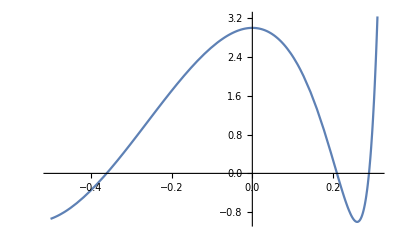

```mathematica
Plot[ComplexExpand[FullSimplify[Subscript[T, 5][A[s],B[s]],s∈Reals]],{s,-1/2,31/100}]
```

```mathematica
NSolve[ComplexExpand[FullSimplify[Subscript[T, 5][A[s],B[s]],s∈Reals]]==-1,s]
```

{{s→0.890388-0.312405 ⅈ},{s→0.890388-0.312405 ⅈ},{s→0.890388+0.312405 ⅈ},{s→0.890388+0.312405 ⅈ},{s→-0.540509},{s→-0.540509},{s→0.259733},{s→0.259733}}

```mathematica
l[s_]:=((-3+4 s (3-6 s^2+4 s^3)) (-1+4 s (1+2 (-1+s) s (-1+2 s))))/(1-2 s)^4;
```

```mathematica
l[.26]
```

-0.999946

```mathematica
FullSimplify[ComplexExpand[FullSimplify[Subscript[T, 5][A[s],B[s]],s∈Reals]]-FullSimplify[PU/.USub[{-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,0}]]]
```

0

### Symbolic Fixed Point Locus: x=z, X=Z,v=v,t=y,T=-Y and thus we have points (x,X,y,Y,x,X,y,-Y,v).

#### The above gives symbolic and complete solutions to the fixed point families!!!!

```mathematica
Expand[CATSU3[{x,X,y,Y,z,Z,t,T,v}]]
```

{z,Z,t-x y-X Y+y z-Y Z,T-X y+x Y+Y z+y Z,x+t z-y z-x y z-X Y z+y z^2-T Z+X y Z-Y Z-x Y Z-2 Y z Z-y Z^2,-X+T z-X y z-Y z+x Y z+Y z^2+t Z+y Z-x y Z-X Y Z+2 y z Z-Y Z^2,y,-Y,v}

```mathematica
Expand[CATSU3[{x,X,y,Y,x,X,y,-Y,v}]]
```

{x,X,y-2 X Y,-Y+2 x Y,x-4 x X Y,-X+2 X y-2 x Y+2 x^2 Y-2 X^2 Y,y,-Y,v}

```mathematica
Solve[-X+2 X y-2 x Y+2 x^2 Y-2 X^2 Y==X&&-Y+2 x Y==Y&&x-4 x X Y==x&&-Y+2 x Y==Y&&y-2 X Y==y,{x,X,y,Y}]
```

{{x→1,X→0},{X→0,Y→0},{y→1,Y→0}}

## Step 5: Jets of Cat map at a given level.

## Defining the Series: u_5=0 and PU=l and l^2=QU and P^2-4Q=0 (iff PU^2-QU=0).

### At a given s (find l after), we need to solve to 2 variables, then define CAT as a map from ℝ^6 to ℝ^6.

```mathematica
$Assumptions=x∈Reals&&X∈Reals&&y∈Reals&&Y∈Reals&&z∈Reals&&Z∈Reals&&t∈Reals&&T∈Reals &&s∈Reals;
```

```mathematica
v4[s_]:=v4[s]=u[-4]/.Solve[PU==l[s],u[-4]][[1]]/.URNS//FullSimplify;
u4[s_]:=u4[s]=u[4]/.Solve[PU==l[s],u[4]][[1]]/.URNS//FullSimplify;
v3[s_]:=v3[s]=u[-3]/.Solve[PU==l[s],u[-3]][[1]]/.URNS//FullSimplify;
u3[s_]:=u3[s]=u[3]/.Solve[PU==l[s],u[3]][[1]]/.URNS//FullSimplify;
```

```mathematica
UHomNew[s_]:={-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,-1+4 s^2,0,-1+(4 s^2)/(1-2 s)^2,0,0};
```

```mathematica
FixedPointSub:={x->UHomNew[s][[1]],X->UHomNew[s][[2]],y->UHomNew[s][[3]],Y->UHomNew[s][[4]],z->UHomNew[s][[5]],Z->UHomNew[s][[6]],t->UHomNew[s][[7]],T->UHomNew[s][[8]]};
```

```mathematica
Discv4atFixed=(3+6/(1-2 s)^4+(16 (-1+s) s (3+8 (-1+s) s^2 (3+s (-1+4 (-1+s) s))))/(1-2 s)^4-t^2-X^2-y^2-x^2 (1+y^2)-Y^2-X^2 Y^2+2 t (x y+X Y)-2 X Y z-z^2+2 X y Z-Z^2+2 x (-X y Y+y z+Y Z))/.FixedPointSub//Simplify
Discu4atFixed=(3+6/(1-2 s)^4+(16 (-1+s) s (3+8 (-1+s) s^2 (3+s (-1+4 (-1+s) s))))/(1-2 s)^4-T^2-y^2-X^2 (1+y^2)-Y^2+2 T (X y-x Y)-x^2 (1+Y^2)-2 X Y z-z^2+2 X y Z-Z^2+2 x (X y Y+y z+Y Z))/.FixedPointSub//Simplify
Discv3atFixed=(3+6/(1-2 s)^4+(16 (-1+s) s (3+8 (-1+s) s^2 (3+s (-1+4 (-1+s) s))))/(1-2 s)^4-t^2-T^2-x^2-X^2+2 T X y-y^2-x^2 y^2-2 T x Y+2 x X y Y-Y^2-X^2 Y^2+2 t (x y+X Y)+2 x y z-2 X Y z-z^2)/.FixedPointSub//Simplify
Discu3atFixed=(3+6/(1-2 s)^4+(16 (-1+s) s (3+8 (-1+s) s^2 (3+s (-1+4 (-1+s) s))))/(1-2 s)^4-t^2-T^2-x^2-y^2-X^2 (1+y^2)-2 x X y Y-Y^2-x^2 Y^2+2 T (X y-x Y)+2 t (x y+X Y)+2 X y Z+2 x Y Z-Z^2)/.FixedPointSub//Simplify
```

0

(4 (1-4 s-2 s^2+8 s^3)^2)/(1-2 s)^4

0

(4 (1-2 s-6 s^2+4 s^3)^2)/(1-2 s)^2

#### So the discriminant for u[-3] and u[-4] are 0 but not for u[3] nor u[4]. But perhaps this should have been predicted since the fixed points are real and the negative indexed coordinates are the imaginary parts. So the jets will be singular at u[-3] and u[-4] at fixed points on the real line.

```mathematica
u4[s]
```

x y+X Y-√(3+6/(1-2 s)^4+(16 (-1+s) s (3+8 (-1+s) s^2 (3+s (-1+4 (-1+s) s))))/(1-2 s)^4-T^2-y^2-X^2 (1+y^2)-Y^2+2 T (X y-x Y)-x^2 (1+Y^2)-2 X Y z-z^2+2 X y Z-Z^2+2 x (X y Y+y z+Y Z))

```mathematica
Expand[2PU/.URNS]
```

-3+t^2+T^2+x^2+X^2-2 t x y-2 T X y+y^2+x^2 y^2+X^2 y^2+2 T x Y-2 t X Y+Y^2+x^2 Y^2+X^2 Y^2-2 x y z+2 X Y z+z^2-2 X y Z-2 x Y Z+Z^2

### We can use Mathematica to directly compute the third jet of u4 as follows:

```mathematica
Localu4[n_][s_]:=Normal[Series[u4[s],{x,UHomNew[s][[1]],n},{X,UHomNew[s][[2]],n},{y,UHomNew[s][[3]],n},{Y,UHomNew[s][[4]],n},{z,UHomNew[s][[5]],n},{Z,UHomNew[s][[6]],n},{T,UHomNew[s][[8]],n}]]
```

```mathematica
Localu4[3][.26]
```

$Aborted

```mathematica
l[.26]
```

-0.999946

### But the routine by Mathematica is in inefficient so below we write our own computation to save computation time. In the end, reducing by one variable is easy. The second one is the hard part, where we need to use implicit differentiation to get the third jet of u3 after subbing u4 into an implicit equation (we have two to work with). First we try to solve for u[3] explicitly after subbing.

```mathematica
HS:=HS=(PU^2-QU)/.URNS//FullSimplify;
```

```mathematica
Variables[HS]
```

{t,T,x,X,y,Y,z,Z}

```mathematica
HSSub:=HSSub=(HS/.{t->u4[s]})//Simplify;
```

```mathematica
Variables[HSSub]
```

{s,T,x,X,y,Y,z,Z}

```mathematica
Solve[HSSub==0,z]
```

#### The above attempt ran for days with my processors at 100% with no output. We just killed the attempt.

### Use implicit differentiation to find the Taylor series locally for just u3 and u4 and sub local expansion into formula (which is otherwise polynomial). Need to use both implicit formulas (one you can solve for explicitly ...but might be easier to just get series for it locally and sub).

### f(x,y,z)=f(x_0, y_0, z_0)+(∂f_0)/(∂x)(x−x_0)+(∂f_0)/(∂y)(y−y_0)+(∂f_0)/(∂z)(z−z_0) +1/2((∂^2 f_0)/(∂x^2)(x−x_0)^(.b2)+(∂^2 f_0)/(∂y^2)(y−y_0)^2+(∂^2 f_0)/(∂z^2)(z−z_0)^2+2(∂^2 f_0)/(∂x∂y)(x−x_0)(y−y_0)+2(∂^2 f_0)/(∂x∂z)(x−x_0)(z−z_0)+2(∂^2 f_0)/(∂z∂y)(z−z_0)(y−y_0))+...

### Locally CAT should be a graph over six variables, so that w.r.t. implicit differentiation, the partial derivatives of the six variables w.r.t. each other are either 1 or 0. The only exception will be the u3 and u4, which will be treated as locally a function of the other 6. We then sub these jets into the CAT map and compute jet of CAT.

#### Here is the 0th derivative of z at fixed points:

```mathematica
z0[s_]:=UHomNew[s][[5]];
```

```mathematica
z0[s]
```

-1+4 s^2

```mathematica
z0[.26]
```

-0.7296

#### Here we compute the 1st, 2nd, and 3rd derivative of z and t at fixed points:

```mathematica
EnumVariablest={s->a[0],x->a[1],X->a[2],y->a[3],Y->a[4],z->a[5],Z->a[6],T->a[7]};
ReverseEVt={a[1]->x,a[2]->X,a[3]->y,a[4]->Y,a[5]->z,a[6]->Z,a[7]->T};
FixedPointSubEVt:={a[1]->UHomNew[a[0]][[1]],a[2]->UHomNew[a[0]][[2]],a[3]->UHomNew[a[0]][[3]],a[4]->UHomNew[a[0]][[4]],a[5]->UHomNew[a[0]][[5]],a[6]->UHomNew[a[0]][[6]],a[7]->UHomNew[a[0]][[8]]};
UHomLocalt[s_]:={UHomNew[s][[1]],UHomNew[s][[2]],UHomNew[s][[3]],UHomNew[s][[4]],UHomNew[s][[5]],UHomNew[s][[6]],UHomNew[s][[8]]};
EnumVariables={s->a[0],x->a[1],X->a[2],y->a[3],Y->a[4],Z->a[5],T->a[6]};
ReverseEV={a[1]->x,a[2]->X,a[3]->y,a[4]->Y,a[5]->Z,a[6]->T};
HSSubEV=HSSub/.EnumVariables;
FixedPointSubEV:={a[1]->UHomNew[a[0]][[1]],a[2]->UHomNew[a[0]][[2]],a[3]->UHomNew[a[0]][[3]],a[4]->UHomNew[a[0]][[4]],z->UHomNew[a[0]][[5]],a[5]->UHomNew[a[0]][[6]],t->UHomNew[a[0]][[7]],a[6]->UHomNew[a[0]][[8]]};
UHomLocal[s_]:={UHomNew[s][[1]],UHomNew[s][[2]],UHomNew[s][[3]],UHomNew[s][[4]],UHomNew[s][[6]],UHomNew[s][[8]]};
TaylorCoeff[i_][s_]:=TaylorCoeff[i][s]=Dummy[i]/.Solve[(Dt[HSSubEV,a[i]]/.{Dt[z,a[i]]->Dummy[i]}/.FixedPointSubEV//Simplify)==0,Dummy[i]][[1]]/.{a[0]->s}//Simplify;
```

```mathematica
TaylorCoeff[i_,j_][s_]:=TaylorCoeff[i,j][s]=Dummy[i,j]/.Solve[(Dt[Dt[HSSubEV,a[i]],a[j]]/.{Dt[z,a[i]]->TaylorCoeff[i][s],Dt[z,a[j]]->TaylorCoeff[j][s],Dt[Dt[z,a[i]],a[j]]->Dummy[i,j]}/.FixedPointSubEV/.{a[0]->s}//Simplify)==0,Dummy[i,j]][[1]];
```

```mathematica
TaylorCoeff[i_,j_,k_][s_]:=TaylorCoeff[i,j,k][s]=Dummy[i,j,k]/.Solve[(Dt[Dt[Dt[HSSubEV,a[i]],a[j]],a[k]]/.{Dt[z,a[i]]->TaylorCoeff[i][s],Dt[z,a[j]]->TaylorCoeff[j][s],Dt[z,a[k]]->TaylorCoeff[k][s],Dt[Dt[z,a[i]],a[j]]->TaylorCoeff[i,j][s],Dt[Dt[z,a[i]],a[k]]->TaylorCoeff[i,k][s],Dt[Dt[z,a[j]],a[k]]->TaylorCoeff[j,k][s],Dt[Dt[Dt[z,a[i]],a[j]],a[k]]->Dummy[i,j,k]}/.FixedPointSubEV/.{a[0]->s}//Simplify)==0,Dummy[i,j,k]][[1]];
```

#### Now that we have the derivatives for z and t (direct and implicit), we compute the jets:

```mathematica
zJet[s_]:=z0[s]+Sum[TaylorCoeff[i][s]*(a[i]-UHomLocal[s][[i]]),{i,1,6}]+Sum[TaylorCoeff[i,j][s]*(a[i]-UHomLocal[s][[i]])*(a[j]-UHomLocal[s][[j]]),{i,1,6},{j,1,6}]+Sum[TaylorCoeff[i,j,k][s]*(a[i]-UHomLocal[s][[i]])*(a[j]-UHomLocal[s][[j]])*(a[k]-UHomLocal[s][[k]]),{i,1,6},{j,1,6},{k,1,6}]/.ReverseEV;
```

```mathematica
tJet[s_]:=UHomNew[s][[7]]+Sum[(D[u4[s]/.EnumVariablest,a[i]]/.FixedPointSubEVt/.{a[0]->s})*(a[i]-UHomLocalt[s][[i]]),{i,1,7}]+Sum[(D[D[u4[s]/.EnumVariablest,a[i]],a[j]]/.FixedPointSubEVt/.{a[0]->s})*(a[i]-UHomLocalt[s][[i]])*(a[j]-UHomLocalt[s][[j]]),{i,1,7},{j,1,7}]+Sum[(D[D[D[u4[s]/.EnumVariablest,a[i]],a[j]],a[k]]/.FixedPointSubEVt/.{a[0]->s})*(a[i]-UHomLocalt[s][[i]])*(a[j]-UHomLocalt[s][[j]])*(a[k]-UHomLocalt[s][[k]]),{i,1,7},{j,1,7},{k,1,7}]/.ReverseEVt;
```

#### Now we compute the cat map from ℝ^6→ ℝ^6:

```mathematica
Proj926[{x_,X_,y_,Y_,z_,Z_,t_,T_,b_}]:={x,X,y,Y,Z,T};
```

```mathematica
zJet[.249]
tJet[.249]
```

-1.50399+1.28663 T^2-x-5.16029 T^2 (0.751996+x)+2.67381 (0.751996+x)^2-10.7239 (0.751996+x)^3+0.0844526 T X+0.0167138 T (0.751996+x) X+1.22118 X^2-4.71443 (0.751996+x) X^2-0.751996 (0.0158728+y)-0.799416 T^2 (0.0158728+y)+2.0107 (0.751996+x) (0.0158728+y)+2.78895 (0.751996+x)^2 (0.0158728+y)-6.31043 T X (0.0158728+y)-2.56426 X^2 (0.0158728+y)+0.673811 (0.0158728+y)^2+5.45915 (0.751996+x) (0.0158728+y)^2+0.681032 (0.0158728+y)^3-1.93507 T Y+14.6832 T (0.751996+x) Y-1.8878 X Y-0.0867515 (0.751996+x) X Y+0.902415 T (0.0158728+y) Y+3.0885 X (0.0158728+y) Y+1.94383 Y^2-13.0016 (0.751996+x) Y^2-2.78224 (0.0158728+y) Y^2+0.043608 T Z-0.530329 T (0.751996+x) Z+0.0387346 X Z-0.160995 (0.751996+x) X Z+1.16741 T (0.0158728+y) Z-7.39926 X (0.0158728+y) Z+1.7915 Y Z-14.4187 (0.751996+x) Y Z-4.96467 (0.0158728+y) Y Z+1.22016 Z^2-5.07144 (0.751996+x) Z^2-2.46712 (0.0158728+y) Z^2

-0.0158728+35.9596 T^2-27.4865 (0.751996+x)-106566. T^2 (0.751996+x)+27172.4 (0.751996+x)^2-8.05253×10^7 (0.751996+x)^3+1.14156 T X-3383. T (0.751996+x) X+35.9686 X^2-106593. (0.751996+x) X^2-21.6578 (0.0158728+y)-81099.4 T^2 (0.0158728+y)+41359. (0.751996+x) (0.0158728+y)-1.83843×10^8 (0.751996+x)^2 (0.0158728+y)-2790.3 T X (0.0158728+y)-81123.2 X^2 (0.0158728+y)+15752.2 (0.0158728+y)^2-1.39954×10^8 (0.751996+x) (0.0158728+y)^2-3.55259×10^7 (0.0158728+y)^3-54.0829 T Y+160490. T (0.751996+x) Y-52.9413 X Y+162822. (0.751996+x) X Y+121973. T (0.0158728+y) Y+124071. X (0.0158728+y) Y+56.2946 Y^2-166991. (0.751996+x) Y^2-126961. (0.0158728+y) Y^2-27.4707 (0.751996+z)-106566. T^2 (0.751996+z)+54274. (0.751996+x) (0.751996+z)-2.41366×10^8 (0.751996+x)^2 (0.751996+z)-3383. T X (0.751996+z)-106593. X^2 (0.751996+z)+41357. (0.0158728+y) (0.751996+z)-3.67527×10^8 (0.751996+x) (0.0158728+y) (0.751996+z)-1.39954×10^8 (0.0158728+y)^2 (0.751996+z)+160275. T Y (0.751996+z)+163034. X Y (0.751996+z)-166829. Y^2 (0.751996+z)+27172.4 (0.751996+z)^2-2.41366×10^8 (0.751996+x) (0.751996+z)^2-1.83843×10^8 (0.0158728+y) (0.751996+z)^2-8.05253×10^7 (0.751996+z)^3+1.14156 X Z-3383. (0.751996+x) X Z-2790.3 X (0.0158728+y) Z+54.0829 Y Z-160490. (0.751996+x) Y Z-121973. (0.0158728+y) Y Z-3383. X (0.751996+z) Z-160275. Y (0.751996+z) Z+35.9596 Z^2-106566. (0.751996+x) Z^2-81099.4 (0.0158728+y) Z^2-106566. (0.751996+z) Z^2

```mathematica
LocalCAT[s_]:=Proj926[CATSU3[{x,X,y,Y,z,Z,t,T,v}]/.{t->tJet[s]}/.{z->zJet[s]}];
```

```mathematica
LocalCAT[.26][[1]]
LocalCAT[.26][[2]]
LocalCAT[.26][[3]]
LocalCAT[.26][[4]]
LocalCAT[.26][[5]]
LocalCAT[.26][[6]]
```

```mathematica
Variables[LocalCAT[.26]]
```

{T,x,X,y,Y,Z}

```mathematica
tJet[.25]
```

Indeterminate

```mathematica
zJet[.25]
```

Indeterminate

```mathematica
UHomLocalt[.25]
```

{-0.75,0,0.,0,-0.75,0,0}

```mathematica
u4[.25]
```

x y+X Y-0.353553 √(9.-8. T^2-8. y^2+X^2 (-8.-8. y^2)-8. Y^2+T (16. X y-16. x Y)+x^2 (-8.-8. Y^2)-16. X Y z-8. z^2+16. X y Z-8. Z^2+x (16. X y Y+16. y z+16. Y Z))

```mathematica
(9.-8. T^2-8. y^2+X^2 (-8.-8. y^2)-8. Y^2+T (16. X y-16. x Y)+x^2 (-8.-8. Y^2)-16. X Y z-8. z^2+16. X y Z-8. Z^2+x (16. X y Y+16. y z+16. Y Z))/.{x->-0.75,X->0,y->0.,Y->0,z->-0.75,Z->-0,T->-0}
```

0.

#### So s=.25 is singular in the local coordinate system. But we are fine from .239 to .249 where the spectrum is elliptic.

## Step 6 : The A, C, & D matrices from the series .

```mathematica
SeriesVariables={x,X,y,Y,Z,T};
```

```mathematica
AMatrixEntry[s_][i_,j_]:=SeriesCoefficient[LocalCAT[s][[i]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[1]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[2]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[3]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[4]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[5]],Table[{SeriesVariables[[k]],UHomLocal[s][[k]],DiscreteDelta[j-k]},{k,1,6}][[6]]];
```

```mathematica
AMatrix[s_]:=AMatrix[s]=Table[AMatrixEntry[s][i,j],{i,1,6},{j,1,6}];
DMatrix[s_]:=DMatrix[s]=DiagonalMatrix[Eigenvalues[AMatrix[s]]];
CMatrix[s_]:=CMatrix[s]=Transpose[Eigenvectors[AMatrix[s]]];
```

```mathematica
AMatrix[.26]//MatrixForm
```

(-1. | 0 | -0.193049 | 0 | 0 | 0.
0 | 0 | 0 | 0 | 1 | 0
-0.173611 | 0 | -1.57007 | 0 | 0 | 0.
0 | -0.173611 | 0 | -1.4592 | 0.173611 | 1
0 | -0.873333 | 0 | 1.79423 | 0.220556 | -0.7296
0 | 0 | 0 | -1 | 0 | 0)

```mathematica
DMatrix[.26]//MatrixForm
CMatrix[.26]//MatrixForm
```

(-1.62379+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.844348+0.535795 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.844348-0.535795 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.225026+0.974353 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.225026-0.974353 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.946272+0. ⅈ)

(0.295641+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.963384+0. ⅈ
0.+0. ⅈ | 0.384986-0.111841 ⅈ | 0.384986+0.111841 ⅈ | 0.158107-0.684599 ⅈ | 0.158107+0.684599 ⅈ | 0.+0. ⅈ
0.955299+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.268124+0. ⅈ
0.+0. ⅈ | 0.491812-0.312087 ⅈ | 0.491812+0.312087 ⅈ | 0.0495133+0.0622516 ⅈ | 0.0495133-0.0622516 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.265138+0.300706 ⅈ | -0.265138-0.300706 ⅈ | 0.702619+0. ⅈ | 0.702619+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.582475+0. ⅈ | 0.582475+0. ⅈ | -0.0717968+0.0342352 ⅈ | -0.0717968-0.0342352 ⅈ | 0.+0. ⅈ)

```mathematica
Inverse[CMatrix[.249]].AMatrix[.249].CMatrix[.249]//MatrixForm
DMatrix[.249]//MatrixForm
```

(-0.737628+0.675208 ⅈ | -1.34812×10^-16+5.55112×10^-16 ⅈ | 2.77556×10^-17+1.04083×10^-16 ⅈ | -3.81639×10^-17+1.23165×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-1.3525×10^-17-4.44089×10^-16 ⅈ | -0.737628-0.675208 ⅈ | -3.64292×10^-17-1.11022×10^-16 ⅈ | 2.94903×10^-17-1.07553×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
-7.21645×10^-16+5.27356×10^-16 ⅈ | 4.44089×10^-16-3.05311×10^-16 ⅈ | -0.0242729+0.999705 ⅈ | 4.25007×10^-17+4.2891×10^-16 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
5.82867×10^-16+3.05311×10^-16 ⅈ | -7.49401×10^-16-5.27356×10^-16 ⅈ | 5.37764×10^-17-4.28477×10^-16 ⅈ | -0.0242729-0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032+0.10909 ⅈ | 5.55112×10^-17-3.46945×10^-18 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.11022×10^-16-3.46945×10^-18 ⅈ | -0.994032-0.10909 ⅈ)

(-0.737628+0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.737628-0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.0242729+0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0242729-0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032+0.10909 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032-0.10909 ⅈ)

```mathematica
Table[Table[Norm[DMatrix[.24+j*.001][[i,i]]],{i,1,6}],{j,-5,9}]
```

{{1.25715,1.25715,1.,1.,0.79545,0.79545},{1.2178,1.2178,1.,1.,0.821151,0.821151},{1.17146,1.17146,1.,1.,0.853638,0.853638},{1.11062,1.11062,1.,1.,0.9004,0.9004},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.,1.}}

```mathematica
Table[Norm[DMatrix[.231][[i,i]]],{i,1,6}]
```

{1.38107,1.38107,1.,1.,0.724074,0.724074}

```mathematica
Table[Norm[DMatrix[.238][[i,i]]],{i,1,6}]
```

{1.11062,1.11062,1.,1.,0.9004,0.9004}

```mathematica
Table[Norm[DMatrix[.239][[i,i]]],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
Table[Norm[DMatrix[.249][[i,i]]],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
Table[Norm[DMatrix[.251][[i,i]]],{i,1,6}]
```

{1.12542,1.,1.,1.,1.,0.906394}

```mathematica
Table[Norm[DMatrix[.26][[i,i]]],{i,1,6}]
```

{1.62379,1.,1.,1.,1.,0.946272}

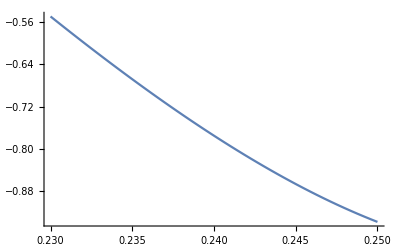

```mathematica
Plot[l[s],{s,.23,.25}]
```

```mathematica
l[.239]
l[.249]
```

-0.754693

-0.925013

```mathematica
LocalCAT[.25]
```

{Indeterminate,Z,Indeterminate,Indeterminate,Indeterminate,-Y}

## Step 7 : Change coordinates w/ C for domain & codomain.

```mathematica
Sub[i_][s_]:=Sub[i][s]=SeriesVariables[[i]]->(CMatrix[s].Table[SeriesVariables[[j]]-UHomLocal[s][[j]],{j,1,6}])[[i]]+UHomLocal[s][[i]];
```

```mathematica
Table[Sub[i][.26],{i,1,6}]
```

{x→(-0.7296+0. ⅈ)+(0.963384+0. ⅈ) T+(0.295641+0. ⅈ) (0.7296+x),X→(0.+0. ⅈ)+(0.384986-0.111841 ⅈ) X+(0.384986+0.111841 ⅈ) (-0.173611+y)+(0.158107-0.684599 ⅈ) Y+(0.158107+0.684599 ⅈ) Z,y→(0.173611+0. ⅈ)-(0.268124+0. ⅈ) T+(0.955299+0. ⅈ) (0.7296+x),Y→(0.+0. ⅈ)+(0.491812-0.312087 ⅈ) X+(0.491812+0.312087 ⅈ) (-0.173611+y)+(0.0495133+0.0622516 ⅈ) Y+(0.0495133-0.0622516 ⅈ) Z,Z→(0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(0.265138+0.300706 ⅈ) (-0.173611+y)+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z,T→(0.+0. ⅈ)+(0.582475+0. ⅈ) X+(0.582475+0. ⅈ) (-0.173611+y)-(0.0717968-0.0342352 ⅈ) Y-(0.0717968+0.0342352 ⅈ) Z}

```mathematica
LocalCATPreSub[s_]:=LocalCATPreSub[s]=LocalCAT[s]/.Table[Sub[i][s],{i,1,6}]
```

```mathematica
LocalCATPreSub[.26]
```

{(-0.7296+0. ⅈ)-(0.963384+0. ⅈ) T-(0.295641+0. ⅈ) (0.7296+x)+50+8.58433 (1) (1) (6+(19+1) Z)+0.546023 ((0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(20+1) 1+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z)^2-11.6081 ((0.+0. ⅈ)+(0.963384+0. ⅈ) T+(0.295641+0. ⅈ) (0.7296+x)) ((0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(0.265138+0.300706 ⅈ) (-0.173611+y)+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z)^2-14.1453 ((0.+0. ⅈ)-(0.268124+0. ⅈ) T+(0.955299+0. ⅈ) (0.7296+x)) ((0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(0.265138+0.300706 ⅈ) (-0.173611+y)+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z)^2,4,1}
 |  |  |  |

```mathematica
LocalCATPostSub[s_]:=LocalCATPostSub[s]=Inverse[CMatrix[s]].Table[LocalCATPreSub[s][[j]]-SeriesCoefficient[LocalCATPreSub[s][[j]],{SeriesVariables[[1]],UHomLocal[s][[1]],0},{SeriesVariables[[2]],UHomLocal[s][[2]],0},{SeriesVariables[[3]],UHomLocal[s][[3]],0},{SeriesVariables[[4]],UHomLocal[s][[4]],0},{SeriesVariables[[5]],UHomLocal[s][[5]],0},{SeriesVariables[[6]],UHomLocal[s][[6]],0}],{j,1,6}];
```

```mathematica
LocalCATPostSub[.26]
```

{(0.+0. ⅈ)+(0.268234+0. ⅈ) ((0.+2.56834×10^-18 ⅈ)-(0.963384+0. ⅈ) T-(0.295641+0. ⅈ) (0.7296+x)+51+0.546023 (6+1)^2-11.6081 ((0.+0. ⅈ)+(0.963384+0. ⅈ) T+(0.295641+0. ⅈ) (0.7296+x)) ((0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(0.265138+0.300706 ⅈ) (-0.173611+y)+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z)^2-14.1453 ((0.+0. ⅈ)-(0.268124+0. ⅈ) T+(0.955299+0. ⅈ) (0.7296+x)) ((0.+0. ⅈ)-(0.265138-0.300706 ⅈ) X-(0.265138+0.300706 ⅈ) (-0.173611+y)+(0.702619+0. ⅈ) Y+(0.702619+0. ⅈ) Z)^2)+(0.963781+0. ⅈ) ((0.-6.96145×10^-18 ⅈ)-1.83431 ((0.+0. ⅈ)+(0.963384+0. ⅈ) T+(0.295641+0. ⅈ) (0.7296+x))+92),4,(0.+0. ⅈ)+(1) 1-(0.295763+0. ⅈ) (1)}
 |  |  |  |

```mathematica
SeriesVariables
```

{x,X,y,Y,Z,T}

```mathematica
SCLCPS[s_][i_][m_]:=SeriesCoefficient[LocalCATPostSub[s][[i]],{SeriesVariables[[1]],UHomLocal[s][[1]],m[[1]]},{SeriesVariables[[2]],UHomLocal[s][[2]],m[[2]]},{SeriesVariables[[3]],UHomLocal[s][[3]],m[[3]]},{SeriesVariables[[4]],UHomLocal[s][[4]],m[[4]]},{SeriesVariables[[5]],UHomLocal[s][[5]],m[[5]]},{SeriesVariables[[6]],UHomLocal[s][[6]],m[[6]]}];
```

```mathematica
Table[SCLCPS[.249][i][{0,0,0,0,0,0}],{i,1,6}]
```

{-6.01946×10^-21-1.97347×10^-20 ⅈ,6.23285×10^-20+7.14199×10^-21 ⅈ,-5.58471×10^-19-1.07307×10^-18 ⅈ,-5.09466×10^-19-1.10371×10^-18 ⅈ,5.58623×10^-17-2.97292×10^-18 ⅈ,5.63688×10^-17+2.97071×10^-18 ⅈ}

```mathematica
Table[SCLCPS[.249][i][SB[[j]]],{i,1,6},{j,1,6}]//MatrixForm
DMatrix[.249]//MatrixForm
```

(-0.737628+0.675208 ⅈ | -7.02563×10^-16+8.06646×10^-16 ⅈ | 2.60209×10^-17+1.07553×10^-16 ⅈ | -3.81639×10^-17+1.12757×10^-16 ⅈ | 3.97977×10^-22+1.06431×10^-22 ⅈ | 3.65422×10^-22+1.9021×10^-22 ⅈ
-3.7817×10^-16-3.1572×10^-16 ⅈ | -0.737628-0.675208 ⅈ | -3.98986×10^-17-1.11022×10^-16 ⅈ | 2.9924×10^-17-1.00614×10^-16 ⅈ | -3.65422×10^-22+1.9021×10^-22 ⅈ | -3.97977×10^-22+1.06431×10^-22 ⅈ
-1.33227×10^-15+1.52656×10^-16 ⅈ | 8.88178×10^-16-8.88178×10^-16 ⅈ | -0.0242729+0.999705 ⅈ | 1.31839×10^-16+5.55112×10^-16 ⅈ | -9.76054×10^-21+1.07117×10^-21 ⅈ | -9.76054×10^-21-1.07117×10^-21 ⅈ
9.99201×10^-16+9.29812×10^-16 ⅈ | -1.33227×10^-15-3.05311×10^-16 ⅈ | 6.59195×10^-17-2.22045×10^-16 ⅈ | -0.0242729-0.999705 ⅈ | 9.76054×10^-21-1.07117×10^-21 ⅈ | 9.76054×10^-21+1.07117×10^-21 ⅈ
1.61255×10^-16+1.97119×10^-16 ⅈ | -5.56782×10^-16-1.19293×10^-16 ⅈ | 1.34528×10^-17+2.56464×10^-16 ⅈ | 3.43993×10^-17+8.72872×10^-16 ⅈ | -0.994032+0.10909 ⅈ | -4.44089×10^-16-6.80012×10^-15 ⅈ
-1.5634×10^-16-1.95357×10^-16 ⅈ | 5.57789×10^-16+1.15193×10^-16 ⅈ | -1.62185×10^-17-2.56364×10^-16 ⅈ | -4.36243×10^-17-8.72541×10^-16 ⅈ | 1.16573×10^-15-5.59275×10^-15 ⅈ | -0.994032-0.10909 ⅈ)

(-0.737628+0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.737628-0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.0242729+0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0242729-0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032+0.10909 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032-0.10909 ⅈ)

## Step 8 : The η & ζ subs.

```mathematica
LocalCATSub[s_]:=LocalCATSub[s]=LocalCATPostSub[s]/.{SeriesVariables[[1]]->(Subscript[ζ, 1]+Subscript[η, 1])/2+UHomLocal[s][[1]],SeriesVariables[[2]]->(Subscript[ζ, 1]-Subscript[η, 1])/(2I)+UHomLocal[s][[2]],SeriesVariables[[3]]->(Subscript[ζ, 2]+Subscript[η, 2])/2+UHomLocal[s][[3]],SeriesVariables[[4]]->(Subscript[ζ, 2]-Subscript[η, 2])/(2I)+UHomLocal[s][[4]],SeriesVariables[[5]]->(Subscript[ζ, 3]+Subscript[η, 3])/2+UHomLocal[s][[5]],SeriesVariables[[6]]->(Subscript[ζ, 3]-Subscript[η, 3])/(2I)+UHomLocal[s][[6]]}//Expand;
```

```mathematica
LocalCATSub[.249]
```

{(-2.91791×10^-22-1.13384×10^-22 ⅈ)-(0.368814-0.337604 ⅈ) ζ_1-(0.0187071-0.0170806 ⅈ) ζ_1^3-(0.375944+0.853797 ⅈ) ζ_1^5+(27.7037-12.1985 ⅈ) ζ_1^7+(6.76542×10^-17+6.59195×10^-17 ⅈ) ζ_2+(0.0749576-0.0846529 ⅈ) ζ_1^2 ζ_2+(3.48327+7.91077 ⅈ) ζ_1^4 ζ_2-(456.797-201.137 ⅈ) ζ_1^6 ζ_2+(0.276842-0.299213 ⅈ) ζ_1 ζ_2^2+(7.92325+17.9943 ⅈ) ζ_1^3 ζ_2^2+(665.597-293.076 ⅈ) ζ_1^5 ζ_2^2-(0.0101121-0.000616041 ⅈ) ζ_2^3-(65.3313+148.372 ⅈ) ζ_1^2 ζ_2^3+4952+(2.60917×10^7-6.71463×10^7 ⅈ) ζ_2 η_1 η_2 η_3^7-(4.37442×10^7+1.69981×10^7 ⅈ) η_1^2 η_2 η_3^7-(1.76169×10^7-4.53366×10^7 ⅈ) ζ_1 η_2^2 η_3^7+(2.79195×10^7-7.18501×10^7 ⅈ) ζ_2 η_2^2 η_3^7-(7.25031×10^7+2.81733×10^7 ⅈ) η_1 η_2^2 η_3^7-(6.50655×10^7+2.52832×10^7 ⅈ) η_2^3 η_3^7+(2.28933×10^7+5.19925×10^7 ⅈ) ζ_1 η_3^8+(2.51167×10^7+5.70419×10^7 ⅈ) ζ_2 η_3^8-(5.09269×10^8+1.97892×10^8 ⅈ) ζ_1 ζ_3 η_3^8-(5.58728×10^8+2.17111×10^8 ⅈ) ζ_2 ζ_3 η_3^8+(1.7604×10^7-7.75138×10^6 ⅈ) η_1 η_3^8-(6.70035×10^7-1.72432×10^8 ⅈ) ζ_3 η_1 η_3^8+(5.43376×10^7-2.3926×10^7 ⅈ) η_2 η_3^8-(2.06818×10^8-5.3224×10^8 ⅈ) ζ_3 η_2 η_3^8+(2.22152×10^7-5.71703×10^7 ⅈ) ζ_1 η_3^9+(2.43728×10^7-6.27226×10^7 ⅈ) ζ_2 η_3^9-(1.93571×10^7+7.52178×10^6 ⅈ) η_1 η_3^9-(5.9749×10^7+2.32173×10^7 ⅈ) η_2 η_3^9,4,(5.60939×10^-17-3.0688×10^-18 ⅈ)-(0.981576-0.0150839 ⅈ) ζ_1^2-(1) ζ_1^4+2979+1-1+(1.06921×10^10-1.06921×10^10 ⅈ) η_3^9}
 |  |  |  |

```mathematica
Variables[LocalCATSub[.249]]
```

{ζ_1,ζ_2,ζ_3,η_1,η_2,η_3}

```mathematica
LocalCATSub[.249]/.{Subscript[ζ, 1]->0,Subscript[ζ, 2]->0,Subscript[ζ, 3]->0,Subscript[η, 1]->0,Subscript[η, 2]->0,Subscript[η, 3]->0}
```

{-2.91791×10^-22-1.13384×10^-22 ⅈ,2.91791×10^-22-1.13384×10^-22 ⅈ,7.46148×10^-21+4.50816×10^-37 ⅈ,-7.46148×10^-21-1.08567×10^-37 ⅈ,5.60939×10^-17+3.0688×10^-18 ⅈ,5.60939×10^-17-3.0688×10^-18 ⅈ}

```mathematica
Table[SCLCS[.249][i][SB[[j]]],{i,1,6},{j,1,6}]//MatrixForm
DMatrix[.249]//MatrixForm
```

(-0.368814+0.337604 ⅈ | -0.368814+0.337604 ⅈ | 6.76542×10^-17+6.59195×10^-17 ⅈ | -4.46691×10^-17+3.20924×10^-17 ⅈ | 0 | 0
-0.337604+0.368814 ⅈ | 0.337604-0.368814 ⅈ | -6.59195×10^-17-6.93889×10^-17 ⅈ | 3.55618×10^-17-4.11997×10^-17 ⅈ | 0 | 0
-5.55112×10^-16 | -1.66533×10^-16+4.44089×10^-16 ⅈ | -0.0121365+0.499853 ⅈ | -0.0121365+0.499853 ⅈ | 0 | 0
0.+5.82867×10^-16 ⅈ | 4.44089×10^-16-1.66533×10^-16 ⅈ | -0.499853+0.0121365 ⅈ | 0.499853-0.0121365 ⅈ | 0 | 0
0 | 0 | 0 | 0 | -0.497016+0.054545 ⅈ | -0.497016+0.054545 ⅈ
0 | 0 | 0 | 0 | -0.054545+0.497016 ⅈ | 0.054545-0.497016 ⅈ)

(-0.737628+0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.737628-0.675208 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.0242729+0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0242729-0.999705 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032+0.10909 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.994032-0.10909 ⅈ)

## Step 9 : α-Matrix and Torsion.

### Notation from paper: 1. d=3 2. F_k^(a_1,...,a_m|b_1,...,b_n) is coefficient of F of total degree k=n+m of the term ζ_a_1...ζ_a_m.η_b_1... η_b_n 3. (...,p_i,q_i,...) for i=1,2,3 are the pairs of component functions LocalCATSub in that order. 4. DMatrix =Diag (...,λ_i, μ_i,...) in order of the diagonal. 5. ϕ and ψ are given by explicit formulae in terms of the eigenvalues in DMatrix and coefficients of p's and q's.

```mathematica
FrequencyVector[s_]:=Table[Norm[Log[DMatrix[s][[i,i]]]/(2Pi*I)],{i,1,6}]
```

```mathematica
FrequencyVector[.249]
```

{0.382027,0.382027,0.253864,0.253864,0.482603,0.482603}

```mathematica
FVnoMultiplicy[s_]:={FrequencyVector[s][[1]],FrequencyVector[s][[3]],FrequencyVector[s][[5]]};
```

#### To test non-planarity: pick 4 values in the elliptic interval, and produce 4 vectors in ℝ^3(3 non-multiplicity values from frequency) and look at translations from one fixed vector to get 3x3 system and take determinant to check if non-planar.

```mathematica
PlanarityTest[s1_,s2_,s3_,s4_]:=Det[{FVnoMultiplicy[s1]-FVnoMultiplicy[s4],FVnoMultiplicy[s2]-FVnoMultiplicy[s4],FVnoMultiplicy[s3]-FVnoMultiplicy[s4]}];
```

```mathematica
LCSVariables={Subscript[ζ, 1],Subscript[η, 1],Subscript[ζ, 2],Subscript[η, 2],Subscript[ζ, 3],Subscript[η, 3]};
```

```mathematica
SB={{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}};
```

```mathematica
SCLCS[s_][i_][m_]:=SeriesCoefficient[LocalCATSub[s][[i]],{LCSVariables[[1]],0,m[[1]]},{LCSVariables[[2]],0,m[[2]]},{LCSVariables[[3]],0,m[[3]]},{LCSVariables[[4]],0,m[[4]]},{LCSVariables[[5]],0,m[[5]]},{LCSVariables[[6]],0,m[[6]]}];
```

```mathematica
pI[i_]:=1/;i==1
pI[i_]:=3/;i==2
pI[i_]:=5/;i==3
qI[i_]:=2/;i==1
qI[i_]:=4/;i==2
qI[i_]:=6/;i==3
```

#### Dictionary:

```mathematica
α[j_,k_][s_]:=α[j,k][s]=Sum[SCLCS[s][pI[j]][SB[[pI[k]]]+SB[[pI[n]]]]*(SCLCS[s][pI[n]][SB[[pI[j]]]+SB[[qI[k]]]])/(DMatrix[s][[pI[j],pI[j]]]*DMatrix[s][[qI[k],qI[k]]]-DMatrix[s][[pI[n],pI[n]]])+SCLCS[s][pI[j]][SB[[pI[n]]]+SB[[pI[j]]]]*(SCLCS[s][pI[n]][SB[[pI[k]]]+SB[[qI[k]]]])/(DMatrix[s][[pI[k],pI[k]]]*DMatrix[s][[qI[k],qI[k]]]-DMatrix[s][[pI[n],pI[n]]])+SCLCS[s][pI[j]][SB[[pI[k]]]+SB[[qI[n]]]]*(SCLCS[s][qI[n]][SB[[pI[j]]]+SB[[qI[k]]]])/(DMatrix[s][[qI[j],qI[j]]]*DMatrix[s][[pI[k],pI[k]]]-DMatrix[s][[qI[n],qI[n]]])+SCLCS[s][pI[j]][SB[[pI[n]]]+SB[[qI[k]]]]*(SCLCS[s][pI[n]][SB[[pI[j]]]+SB[[pI[k]]]])/(DMatrix[s][[pI[j],pI[j]]]*DMatrix[s][[pI[k],pI[k]]]-DMatrix[s][[pI[n],pI[n]]]),{n,1,3}]+Sum[(SCLCS[s][pI[j]][SB[[qI[n]]]+SB[[qI[k]]]]+SCLCS[s][pI[j]][SB[[qI[k]]]+SB[[qI[n]]]])*(SCLCS[s][qI[n]][SB[[pI[k]]]+SB[[pI[j]]]])/(DMatrix[s][[qI[j],qI[j]]]*DMatrix[s][[qI[k],qI[k]]]-DMatrix[s][[qI[n],qI[n]]]),{n,1,3}]+SCLCS[s][pI[j]][SB[[pI[k]]]+SB[[pI[j]]]+SB[[qI[k]]]];
```

```mathematica
AlphaMatrix[s_]:=Table[α[j,k][s],{j,1,3},{k,1,3}];
Torsion[s_]:=Det[AlphaMatrix[s]];
```

```mathematica
AlphaMatrix[.249]//MatrixForm
```

(0.00552244-0.0340402 ⅈ | 0.0107941-0.000895037 ⅈ | 1.27133+2.0689 ⅈ
-0.200044-0.525768 ⅈ | -0.327311-0.329913 ⅈ | -0.800469-0.841658 ⅈ
-4.01094-2.67688 ⅈ | -8.79221-8.77867 ⅈ | 250.545+281.496 ⅈ)

```mathematica
Torsion[.249]
```

-20.077-0.73655 ⅈ

```mathematica
Table[Torsion[.24+j*.001],{j,-1,9}]
```

{-250.764+302.819 ⅈ,-42.4163+62.2363 ⅈ,21.244-8.39023 ⅈ,-0.916166-0.205169 ⅈ,-1.47984-0.719269 ⅈ,-1.9477-1.24885 ⅈ,-2.26812-3.35419 ⅈ,-3.59411-3.87318 ⅈ,-4.51798-3.7802 ⅈ,34.1405+35.5889 ⅈ,-20.077-0.73655 ⅈ}

#### Upshot: torsion is non-zero!!!!!

```mathematica
PlanarityTest[.239,.24,.241,.242]
```

0.0000158782